```mathematica
SetDirectory[NotebookDirectory[]];
<< Italy2018ElectionDataAnalysis.wl;
```

```mathematica
PieChart[PlottingElectionElectorsPie["camera", region-> "BASILICATA"], ChartLegends->{"Votanti maschi", "Votanti femmine"}]
```

-Graphics-

```mathematica
PieChart[PlottingElectionVotersPie["camera", query->"ELETTORI = 13746"], ChartLegends->{"Votanti maschi", "Votanti femmine"}]
```

-Graphics-

```mathematica
PieChart[PlottingElectionVotersNonVotersPie["camera"], ChartLegends->{"Votanti maschi", "Votanti femmine", "Non votanti maschi", "Non votanti femmine"}]
```

-Graphics-

```mathematica
divisions=EntityValue[Entity["AdministrativeDivision",{EntityProperty["AdministrativeDivision","ParentRegion"]->Entity["Country","Italy"]}],"Entities"];
divisionsVotes = Table[Transpose @ {divisions, PlottingElectionRegionCoalitionsBars["camera", coalition] }, {coalition, {"Sinistra", "Centro", "Destra"}}];
GeoRegionValuePlot[Table[rv, {rv,  divisionsVotes}]]
```

-Graphics-

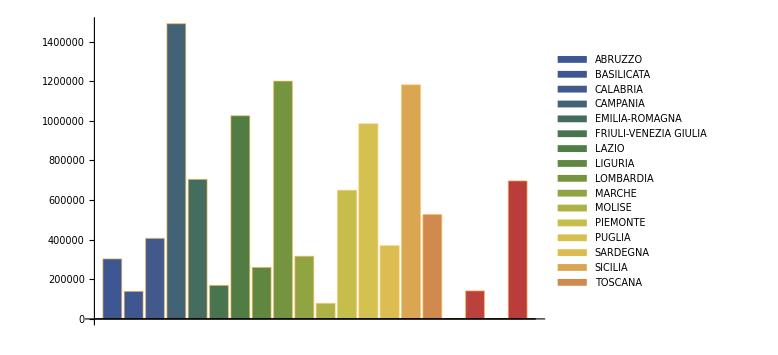

```mathematica
BarChart[PlottingElectionRegionCoalitionsBars["camera", "Centro"], ChartLegends->GetRegions[], ImageSize->Large, ChartStyle->"DarkRainbow"]
```